```mathematica
dx=0.1;
a=1;
dt=0.05;
```

```mathematica
Clear[oscillationEquation]
oscillationEquation[n_]:=Module[{u=Table[Table[0,{x,0,1,dx}],n]},u⟦1⟧=Table[x*(1-x),{x,0,1,dx}]; Do[u⟦2⟧⟦j⟧=u⟦1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(u⟦1⟧⟦j-1⟧+u⟦1⟧⟦j+1⟧),{j,2,10}];Do[Do[u⟦i⟧⟦j⟧=u⟦i-1⟧⟦j⟧*2*(1-(a^2 dt^2)/dx^2)+(a^2 dt^2)/dx^2*(u⟦i-1⟧⟦j-1⟧+u⟦i-1⟧⟦j+1⟧)- u⟦i-2⟧⟦j⟧,{j,2,10}],{i,3,n}];u]
```

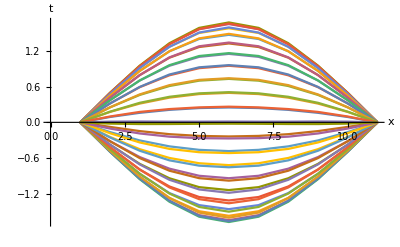

```mathematica
ListLinePlot[oscillationEquation[40],AxesLabel->{"x","t"}]
```